```mathematica
cof:={{1,b1},{a2,b2},{a3,b3},{a4,b4},{a5,0}}
v:={v1,v2,v3,v4,v5}
v1:=0
v2:=0.2
v3:=-0.15
v4:=0.05
v5:=-0.3
eng:=0.1
densityFunction[f_]:=f f*

pot[x_]:=Piecewise[{{v1,x<0},{v2,0<x<10},{v3,10<x<60},{v4,60<x<70},{v5,70<x}}]

expform[zone_,x_]:=Part[Part[cof,zone],1] Exp[I k[zone] x]+Part[Part[cof,zone],2] Exp[-I k[zone] x]
(*decform[zone_,x_]:=Part[Part[cof,zone],1] Exp[k[zone] x]+Part[Part[cof,zone],2] Exp[-k[zone] x]*)

k[zone_]:=Sqrt[(eng-Part[v,zone])/3.81]


result:=Solve[{expform[1,0]==expform[2,0],expform[2,10]==expform[3,10],expform[3,60]==expform[4,60],expform[4,70]==expform[5,70],(D[expform[1,x],x]/.x->0)==(D[expform[2,x],x]/.x->0),(D[expform[2,x],x]/.x->10)==(D[expform[3,x],x]/.x->10),(D[expform[3,x],x]/.x->60)==(D[expform[4,x],x]/.x->60),(D[expform[4,x],x]/.x->70)==(D[expform[5,x],x]/.x->70)},{a2,a3,a4,a5,b1,b2,b3,b4}]
```

```mathematica
result
```

{{a2→1.01189-0.936254 ⅈ,a3→-0.339944-0.0299639 ⅈ,a4→0.314394-0.27522 ⅈ,a5→-0.206734-0.0700589 ⅈ,b1→0.0756405-0.948148 ⅈ,b2→0.0637464-0.0118942 ⅈ,b3→-0.139257+0.191827 ⅈ,b4→0.184647-0.0756858 ⅈ}}

```mathematica
pot[x_]:=Piecewise[{{v1,x<0},{v2,0<x<10},{v3,10<x<60},{v4,60<x<70},{v5,70<x}}]
```

```mathematica
phi[x_]:=Piecewise[{{expform[1,x],x<0},{expform[2,x],0<x<10},{expform[3,x],10<x<60},{expform[4,x],60<x<70},{expform[5,x],70<x}}]/.result[[1]]
```

```mathematica
phi[x]
```

Piecewise[{{(0.0756405-0.948148 ⅈ) ⅇ^((0.-0.162008 ⅈ) x)+ⅇ^((0.+0.162008 ⅈ) x), x<0}, {(1.01189-0.936254 ⅈ) ⅇ^((-0.162008+0. ⅈ) x)+(0.0637464-0.0118942 ⅈ) ⅇ^((0.162008+0. ⅈ) x), 0<x<10}, {(-0.139257+0.191827 ⅈ) ⅇ^((0.-0.256158 ⅈ) x)-(0.339944+0.0299639 ⅈ) ⅇ^((0.+0.256158 ⅈ) x), 10<x<60}, {(0.184647-0.0756858 ⅈ) ⅇ^((0.-0.114557 ⅈ) x)+(0.314394-0.27522 ⅈ) ⅇ^((0.+0.114557 ⅈ) x), 60<x<70}, {(-0.206734-0.0700589 ⅈ) ⅇ^((0.+0.324017 ⅈ) x), 70<x}, {0, True}}]

```mathematica
phi[x_]:=Piecewise[{{(0.07564053115514274-0.9481477822861708 ⅈ) ⅇ^((0.-0.1620083922520836 ⅈ) x)+ⅇ^((0.+0.1620083922520836 ⅈ) x), x<0}, {(1.011894156720657-0.9362536255655141 ⅈ) ⅇ^((-0.1620083922520836+0. ⅈ) x)+(0.06374637443448593-0.011894156720656872 ⅈ) ⅇ^((0.1620083922520836+0. ⅈ) x), 0<x<10}, {(-0.13925669700842763+0.19182729306103152 ⅈ) ⅇ^((0.-0.25615775978927996 ⅈ) x)-(0.33994367720730584+0.029963930414182494 ⅈ) ⅇ^((0.+0.25615775978927996 ⅈ) x), 10<x<60}, {(0.18464696336405292-0.07568578303468572 ⅈ) ⅇ^((0.-0.11455723277057846 ⅈ) x)+(0.3143935292274079-0.27521996508185753 ⅈ) ⅇ^((0.+0.11455723277057846 ⅈ) x), 60<x<70}, {(-0.20673386895736978-0.07005893177967341 ⅈ) ⅇ^((0.+0.3240167845041672 ⅈ) x), 70<x}, {0, True}}]
```

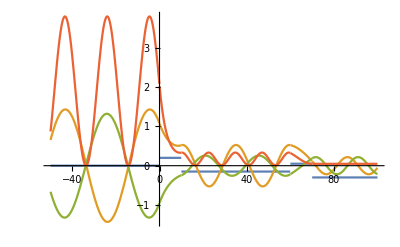

```mathematica
Plot[{pot[x],Re[phi[x]],Im[phi[x]],densityFunction[phi[x]]},{x,-50,100},PlotRange->Full]
```

```mathematica
phi[100]
```

-0.0557587-0.211041 ⅈ

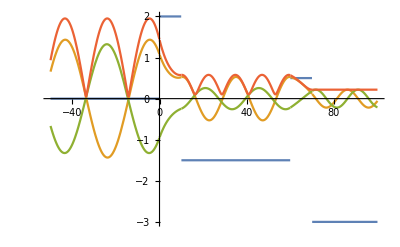

```mathematica
Plot[{pot[x]10,Re[phi[x]],Im[phi[x]],Sqrt[densityFunction[phi[x]]]},{x,-50,100},PlotRange->Full]
```

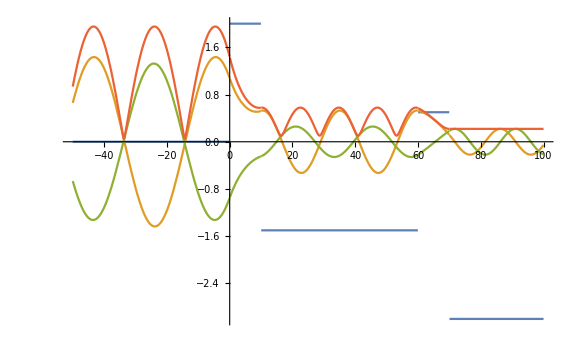

```mathematica
Show[%73,ImageSize->Large]
```

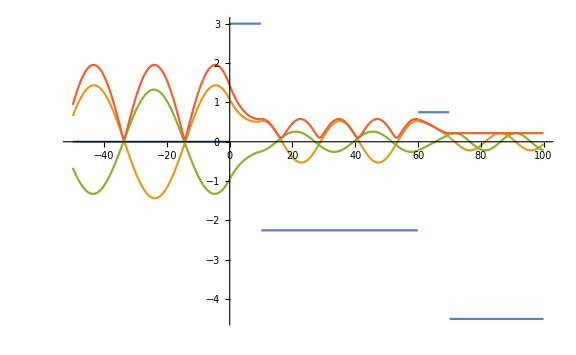

```mathematica
Show[%70,ImageSize->Large]
```

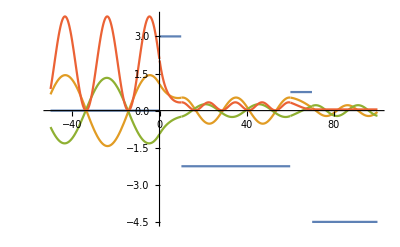

```mathematica
Show[%53,ImageSize->Full]
```

```mathematica
resultcof:= cof/. result
```

```mathematica
resultcof:= Part[cof/. result,1]
```

```mathematica
getConst[zone_,const_]:=Part[Part[resultcof,zone],const]
```

```mathematica
getConst[5,1]
```

-0.206734-0.0700589 ⅈ

```mathematica
Sqrt[densityFunction[getConst[5,1]]]/1 + Sqrt[densityFunction[getConst[1,2]]]/1
```

1.16944+0. ⅈ